## General Settings

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
dat6dFGS=Import["6dFGS.csv","Data",SkipLines->1];(*RA|DEC|z|ID*)
ndat6dFGS=Length[dat6dFGS]
tab6dFGS=Table[{dat6dFGS[[i,1]],dat6dFGS[[i,2]],dat6dFGS[[i,3]]},{i,1,ndat6dFGS}];
listz=Flatten[Table[{dat6dFGS[[i,3]]},{i,1,ndat6dFGS}]];
c=3 10^5;   
listzkm=c listz;
(*Stores equatorial coordinates while converting to decimal degrees*)
dchi[nsig_,M_]:=2 InverseGammaRegularized[M/2,1-Erf[nsig/(√2)]]//N
tabcoord=Table[{FromDMS[dat6dFGS[[i,1]]]*15,FromDMS[dat6dFGS[[i,2]]]},{i,1,ndat6dFGS}];
ticksy={{-1.5707963267948966,-90" °"},{-1.27,-75" °"},{-1.07,-60" °"},{-0.835,-45" °"},{-0.57,-30" °"},{-0.28,-15" °"},{0.29,15" °"},{0.57,30" °"},{0.835,45" °"},{1.07,60" °"},{1.285,75" °"}};
ticksx={{-2.82,0" °"},{-2.36,30" °"},{-1.89,60" °"},{-1.42,90" °"},{-0.949,120" °"},{-0.47,150" °"},{0.479,210" °"},{0.94,240" °"},{1.41,270" °"},{1.89,300" °"},{2.35,330" °"},{2.82,360" °"}};
```

3015

## Redshift Analysis

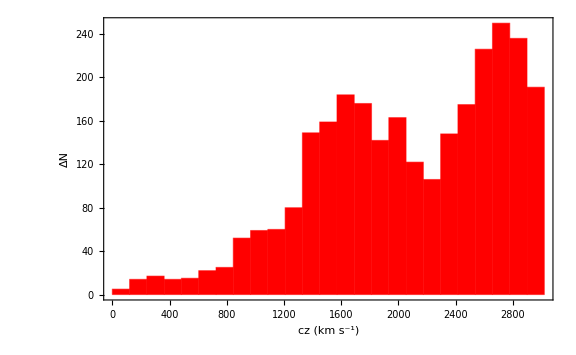

```mathematica
plhist=Histogram[Select[listzkm,#>=100&],{"Raw",25},ChartStyle->Red,Frame->True,FrameLabel->{"cz (km s^-1)","ΔN"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],ImageSize->Large]
```

```mathematica
Export[NotebookDirectory[]<>"Histogram_6dFGS.pdf",plhist,ImageResolution->1000];
```

### χ^2 Minimization Process

```mathematica
listzkmbins=BinLists[Select[listzkm,#>=100 &],120];
ogsublengths=Map[Length,listzkmbins,{1}];
Length[ogsublengths]
```

25

```mathematica
Length[Select[listzkm,#>=100 &]]
```

2790

```mathematica
(*listdNdatog={};
listdNdat={};
sigma=300;
Do[AppendTo[listdNdatog,{Mean[{listzkmbins[[i,1]],listzkmbins[[i,ogsublengths[[i]]]]}],ogsublengths[[i]]}],{i,1,25}]
Do[AppendTo[listdNdat,{Mean[{listzkmbins[[i,1]],listzkmbins[[i,ogsublengths[[i]]]]}]-RandomVariate[NormalDistribution[0,sigma]],ogsublengths[[i]]}],{i,1,25}]
listdNdat=Drop[listdNdat,1];
listdNdatog=Drop[listdNdatog,1];
listdNdat
listdNdatog*)
```

```mathematica
listdNdat={{601.4682108621225,15},{118.64710837220647,17},{634.6474362318006,14},{573.5334545509221,13},{745.2999399418034,21},{318.22792287442155,26},{853.4849661645247,53},{1148.765992397962,58},{1485.7135580356476,56},{1212.8643826974633,80},{1162.204176698302,145},{1792.0229900107834,151},{1527.3038424919105,179},{1529.160597369631,182},{2353.760433567729,155},{1894.0279783752796,150},{2169.530700632335,133},{2406.918623833039,95},{2619.1107962431233,153},{2609.1405407199763,157},{2813.0339073608034,223},{2485.5369793714813,248},{2609.3991762806427,241},{2921.1553297812666,221}};
listdNdatog={{167.85,15},{298.2,17},{425.55,14},{537.45,13},{654.6,21},{775.5,26},{900.15,53},{1020.3,58},{1140.3,56},{1259.4,80},{1380.6,145},{1501.1999999999998,151},{1619.85,179},{1739.55,182},{1859.85,155},{1982.85,150},{2100.6000000000004,133},{2221.6499999999996,95},{2340.15,153},{2459.7,157},{2580.1499999999996,223},{2699.8500000000004,248},{2820.75,241},{2940.,221}};
test={};
testog={};
Do[AppendTo[testog,listdNdatog[[i,1]]-Mean[{listzkmbins[[i+1,1]],listzkmbins[[i+1,ogsublengths[[i+1]]]]}]],{i,1,24}]
Do[AppendTo[test,listdNdat[[i,1]]-Mean[{listzkmbins[[i+1,1]],listzkmbins[[i+1,ogsublengths[[i+1]]]]}]],{i,1,24}]
test
testog
Length[listdNdat]
Length[listdNdatog]
```

{433.618,-179.553,209.097,36.0835,90.6999,-457.272,-46.665,128.466,345.414,-46.5356,-218.396,290.823,-92.5462,-210.389,493.91,-88.822,68.9307,185.269,278.961,149.441,232.884,-214.313,-211.351,-18.8447}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

24

24

```mathematica
(* Construction of χ^2*)
DN[dN_,dH_,cz_,czt_]:=dN*(cz/listdNdat[[1,1]])^2 (1-dH*HeavisideTheta[cz-czt])^-3;

chi2[dN_,dH_,czt_,s_]:=Sum[(listdNdatog[[i,2]]-DN[dN,dH,listdNdat[[i,1]],czt])^2/(Length[listdNdatog]/listdNdatog[[i,2]]+s^2),{i,1,Length[listdNdat]}];
```

```mathematica
chmin2bf={201670.28207017478,{dN->26.152986704005393,dH->-0.3501396117553435,czt->1668.852155672399}};
```

```mathematica
sbf=NSolve[{chi2[chmin2bf[[2,1,2]],chmin2bf[[2,2,2]],chmin2bf[[2,3,2]],s]==Length[Select[listzkm,#>=100 &]]&&s>0},s]
```

{{s→3.69999}}

```mathematica
(*chminfm=FindMinimum[chi2[dN,dH,czt],{{dN,15},{dH},{czt,1500}}];**)
```

```mathematica
chmin2=NMinimize[{chi2[dN,dH,czt,sbf[[1,1,2]]],dN>0, -0.5<dH<0, 1700<czt && czt<3000},{dN,dH,czt}]
```

{2478.77,{dN→20.9459,dH→-0.275234,czt→1810.85}}

```mathematica
chi2[chmin2bf[[2,1,2]],chmin2bf[[2,2,2]],chmin2bf[[2,3,2]],sbf[[1,1,2]]]
```

2790.

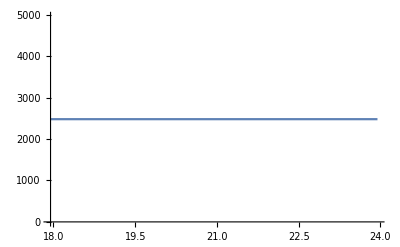

```mathematica
Plot[chi2[chmin2[[2,1,2]],chmin2[[2,2,2]],chmin2[[2,3,2]],sbf[[1,1,2]]],{x,chmin2[[2,1,2]]-3,chmin2[[2,1,2]]+3}]
```

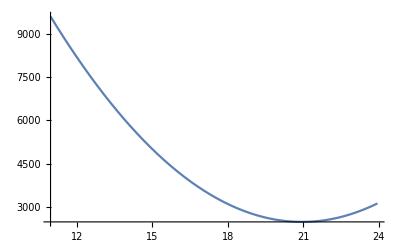

```mathematica
Plot[chi2[x,chmin2[[2,2,2]],chmin2[[2,3,2]],sbf[[1,1,2]]],{x,chmin2[[2,1,2]]-10,chmin2[[2,1,2]]+3}]
```

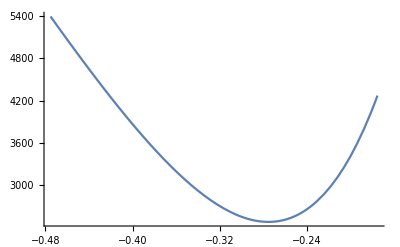

```mathematica
Plot[chi2[chmin2[[2,1,2]],y,chmin2[[2,3,2]],sbf[[1,1,2]]],{y,chmin2[[2,2,2]]-0.2,chmin2[[2,2,2]]+0.1}]
```

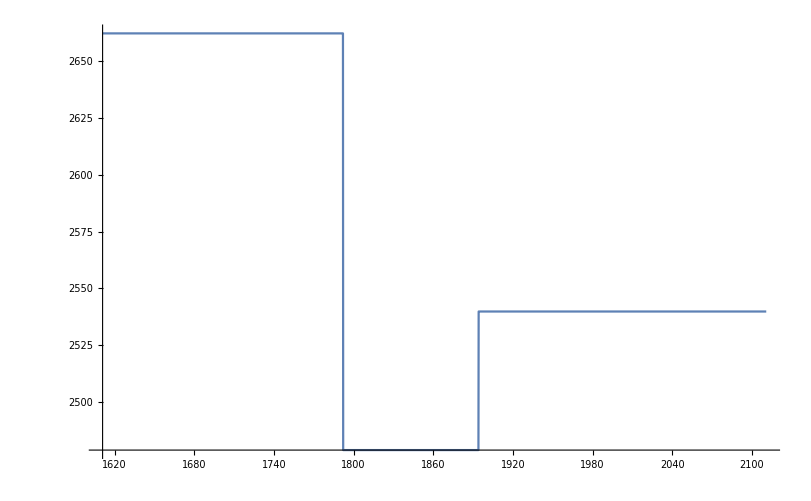

```mathematica
Plot[chi2[chmin2[[2,1,2]],chmin2[[2,2,2]],z,sbf[[1,1,2]]],{z,chmin2[[2,3,2]]-200,chmin2[[2,3,2]]+300}]
```

```mathematica
errdnlist={};
errdnlist=Table[{listdNdatog[[i,1]],Around[listdNdatog[[i,2]],{-(Length[listdNdatog]/listdNdatog[[i,2]]+sbf[[1,1,2]]^2),(Length[listdNdatog]/listdNdatog[[i,2]]+sbf[[1,1,2]]^2)}]},{i,1,Length[listdNdatog]}];
errdnlist2={};
errdnlist2=Table[{listdNdat[[i,1]],Around[listdNdat[[i,2]],{-(Length[listdNdat]/listdNdat[[i,2]]+sbf[[1,1,2]]^2),(Length[listdNdat]/listdNdat[[i,2]]+sbf[[1,1,2]]^2)}]},{i,1,Length[listdNdat]}];
```

```mathematica
pl1=Plot[DN[chmin2[[2,1,2]],chmin2[[2,2,2]],z,chmin2[[2,3,2]]],{z,0,3000},PlotStyle->Blue];
pl2=Histogram[{Select[listzkm,#>=100 &]},25,ChartStyle->Orange,PlotTheme->"Scientific"];
pl3=ListPlot[errdnlist2,PlotStyle->Red];
(*pl4=Plot[nlm[cz],{cz,0,3000},PlotStyle->Red];
Show[pl4,pl3]*)
(*pltrans=Show[pl3,pl1,Frame->True,FrameLabel->{"cz (km s^-1)","dN"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],ImageSize->Large]*)
```

```mathematica
Export[NotebookDirectory[]<>"dN_cz_plot.pdf",pltrans,ImageResolution->1000];
```

```mathematica
chmin2[[2]]
```

{dN→20.9459,dH→-0.275234,czt→1810.85}

```mathematica
dNbf=chmin2[[2,1,2]];
dHbf=chmin2[[2,2,2]];
cztbf=chmin2[[2,3,2]];
sdN=0.1;
dNstep=0.02;
sdH=0.001;
dHstep=0.0001;
chifun=ListInterpolation[ParallelTable[chi2[dN,dH,cztbf,sbf[[1,1,2]]],{dN,dNbf-sdN,dNbf+sdN,dNstep},{dH,dHbf-sdH,dHbf+sdH,dHstep},DistributedContexts->Automatic],{{dNbf-sdN,dNbf+sdN},{dHbf-sdH,dHbf+sdH}}];
(* Params that we want to calculate the errors *)
params={dN,dH};
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
Fij=1/2 Table[D[chifun[dN,dH],params[[p]],params[[d]]]/.chmin2[[2]],{p,1,Length[params]},{d,1,Length[params]}];
cij=Inverse[Fij];
errors=Sqrt[Diagonal[cij]];
Print["The best fit parameters for dN, dH and czt are: dN = ",dNbf," ± ",errors[[1]],", dH = ",dHbf," ± ",errors[[2]]]
```

The best fit parameters for dN, dH and czt are: dN = 20.9459 ± 0.234798, dH = -0.275234 ± 0.00552022

```mathematica
contour=ContourPlot[chi2[dN,dH,cztbf,sbf[[1,1,2]]],{dN,dNbf-1,dNbf+1},{dH,dHbf-0.05,dHbf+0.05},Contours->{chmin2[[1]]+dchi[1,2],chmin2[[1]]+dchi[2,2],chmin2[[1]]+dchi[3,2]},Frame->True,FrameLabel->{"A","ΔH_0/H_0"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],Epilog->{{PointSize[Large],Black,Point[{dNbf,dHbf}]}},ContourShading->{Cyan,RGBColor[0.78,1,0.96],LightCyan, White},PlotRange->{{20,22},{-0.25,-0.3}},ImageSize->650];
```

```mathematica
Export[NotebookDirectory[]<>"dH_dN_cont.pdf",contour,ImageResolution->1000];
```

```mathematica
pl4=Plot[{DN[chmin2[[2,1,2]],chmin2[[2,2,2]],z,chmin2[[2,3,2]]],DN[chmin2[[2,1,2]]+errors[[1]],chmin2[[2,2,2]]+errors[[2]],z,chmin2[[2,3,2]]],DN[chmin2[[2,1,2]]-errors[[1]],chmin2[[2,2,2]]-errors[[2]],z,chmin2[[2,3,2]]]},{z,0,3000},PlotStyle->{Blue,Cyan,Cyan},Filling->{2->{{3},Cyan}}];
pltrans=Show[{pl4,pl1,pl3},Frame->True,FrameLabel->{"cz (km s^-1)","ΔN"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],ImageSize->1000];
```

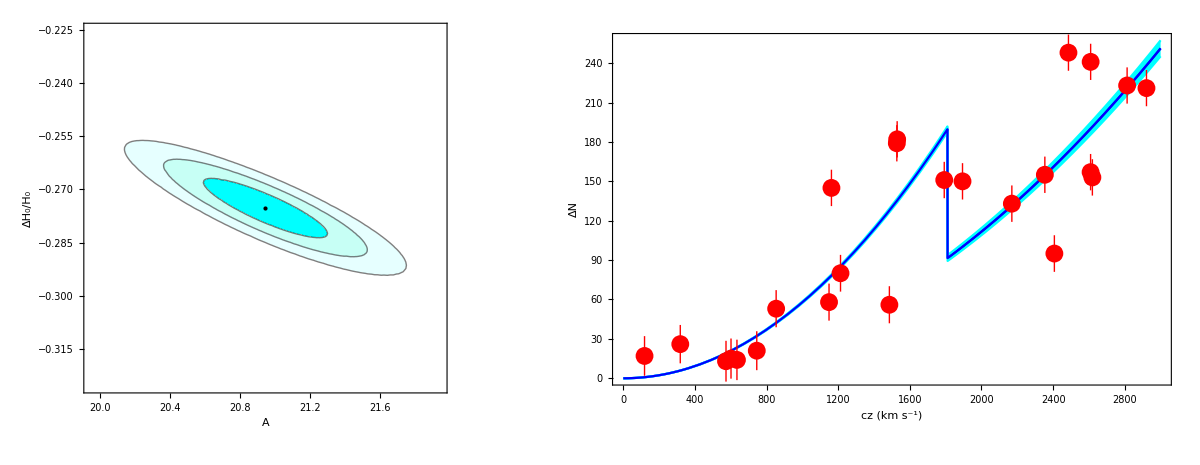

```mathematica
combplt=GraphicsGrid[{{contour,pltrans}},Spacings->-150,ImageSize->1200]
```

```mathematica
Export[NotebookDirectory[]<>"dH_dN__dN_cz_plot.pdf",combplt,ImageResolution->1000];
```

## Sky Coverage of 6dFGS

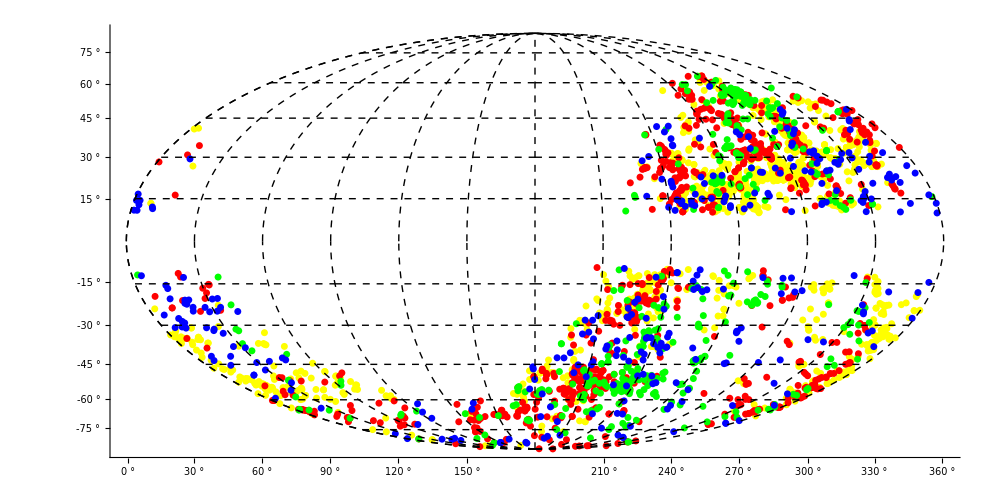

```mathematica
(*Conversion from Equatorial to Galactic coordinates*)
tabcoordgal={};
Do[
sinb=Cos[tabcoord[[i,2]] Degree]Cos[27.4 Degree]Cos[tabcoord[[i,1]] Degree - 192.25 Degree]+Sin[tabcoord[[i,2]] Degree]Sin[27.4 Degree];
b[i]=ArcSin[sinb]/Degree;
y=Sin[tabcoord[[i,2]] Degree]-Sin[b[i] Degree]Sin[27.4 Degree];
x=Cos[tabcoord[[i,2]]Degree] Sin[tabcoord[[i,1]] Degree-192.25 Degree]Cos[27.4 Degree];
l0=ArcTan[y/x]/Degree;
If[y>0 && x>0,l1=l0];
If[y<0 && x>0,l1=l0+360];
If[y>0 && x<0,l1=l0+180];
If[y<0 && x<0,l1=l0+180];
If[y==0 && x>0,l1=0];
If[y==0 && x<0,l1=180];
If[y>0 && x==0,l1=90];
If[y<0 && x==0,l1=270];
l[i]=l1+33;
AppendTo[tabcoordgal,{b[i],l[i]}],{i,1,Length[tabcoord]}]


tab6dFGS025=Select[tab6dFGS,#[[3]]<0.0025&];
tabcoord025=Table[{FromDMS[tab6dFGS025[[i,1]]]*15,FromDMS[tab6dFGS025[[i,2]]]},{i,1,Length[tab6dFGS025]}];

Clear[l,l0,l1,b]
tabcoordgal025={};
Do[
sinb=Cos[tabcoord025[[i,2]] Degree]Cos[27.4 Degree]Cos[tabcoord025[[i,1]] Degree - 192.25 Degree]+Sin[tabcoord025[[i,2]] Degree]Sin[27.4 Degree];
b[i]=ArcSin[sinb]/Degree;
y=Sin[tabcoord025[[i,2]] Degree]-Sin[b[i] Degree]Sin[27.4 Degree];
x=Cos[tabcoord025[[i,2]]Degree] Sin[tabcoord025[[i,1]] Degree-192.25 Degree]Cos[27.4 Degree];
l0=ArcTan[y/x]/Degree;
If[y>0 && x>0,l1=l0];
If[y<0 && x>0,l1=l0+360];
If[y>0 && x<0,l1=l0+180];
If[y<0 && x<0,l1=l0+180];
If[y==0 && x>0,l1=0];
If[y==0 && x<0,l1=180];
If[y>0 && x==0,l1=90];
If[y<0 && x==0,l1=270];
l[i]=l1+33;
AppendTo[tabcoordgal025,{b[i],l[i]}],{i,1,Length[tabcoord025]}];

(*z<0.0025 sample distribution*)
GeoGraphics[{Orange,AbsolutePointSize@5,Point[GeoPosition@tabcoordgal025]},GeoRange->{{-90,90},{0,360}},GeoGridLinesStyle->Directive[Black,Dashed],GeoProjection->"Mollweide",GeoGridLines->{{-90,90,-75,75,-60,60,-45,45,-30,30,-15,15},{0,30,60,90,120,150,180,210,240,270,300,330,360}},ImageSize->1000,Ticks->{ticksx,ticksy},GeoBackground->White,Axes->True,Background->White,AxesStyle->Black,TicksStyle->Directive[Black,FontSize->19]];

tab6dFGS05=Select[tab6dFGS,#[[3]]>=0.0025 && #[[3]]<0.005 &];
tabcoord05=Table[{FromDMS[tab6dFGS05[[i,1]]]*15,FromDMS[tab6dFGS05[[i,2]]]},{i,1,Length[tab6dFGS05]}];

Clear[l,l0,l1,b]
tabcoordgal05={};
Do[
sinb=Cos[tabcoord05[[i,2]] Degree]Cos[27.4 Degree]Cos[tabcoord05[[i,1]] Degree - 192.25 Degree]+Sin[tabcoord05[[i,2]] Degree]Sin[27.4 Degree];
b[i]=ArcSin[sinb]/Degree;
y=Sin[tabcoord05[[i,2]] Degree]-Sin[b[i] Degree]Sin[27.4 Degree];
x=Cos[tabcoord05[[i,2]]Degree] Sin[tabcoord05[[i,1]] Degree-192.25 Degree]Cos[27.4 Degree];
l0=ArcTan[y/x]/Degree;
If[y>0 && x>0,l1=l0];
If[y<0 && x>0,l1=l0+360];
If[y>0 && x<0,l1=l0+180];
If[y<0 && x<0,l1=l0+180];
If[y==0 && x>0,l1=0];
If[y==0 && x<0,l1=180];
If[y>0 && x==0,l1=90];
If[y<0 && x==0,l1=270];
l[i]=l1+33;
AppendTo[tabcoordgal05,{b[i],l[i]}],{i,1,Length[tabcoord05]}];

(*0.0025<=z<0.005 sample distribution*)
GeoGraphics[{Orange,AbsolutePointSize@5,Point[GeoPosition@tabcoordgal05]},GeoRange->{{-90,90},{0,360}},GeoGridLinesStyle->Directive[Black,Dashed],GeoProjection->"Mollweide",GeoGridLines->{{-90,90,-75,75,-60,60,-45,45,-30,30,-15,15},{0,30,60,90,120,150,180,210,240,270,300,330,360}},ImageSize->1000,Ticks->{ticksx,ticksy},GeoBackground->White,Axes->True,Background->White,AxesStyle->Black,TicksStyle->Directive[Black,FontSize->19]];

tab6dFGS075=Select[tab6dFGS,#[[3]]>=0.005 && #[[3]]<0.0075&];
tabcoord075=Table[{FromDMS[tab6dFGS075[[i,1]]]*15,FromDMS[tab6dFGS075[[i,2]]]},{i,1,Length[tab6dFGS075]}];

Clear[l,l0,l1,b]
tabcoordgal075={};
Do[
sinb=Cos[tabcoord075[[i,2]] Degree]Cos[27.4 Degree]Cos[tabcoord075[[i,1]] Degree - 192.25 Degree]+Sin[tabcoord075[[i,2]] Degree]Sin[27.4 Degree];
b[i]=ArcSin[sinb]/Degree;
y=Sin[tabcoord075[[i,2]] Degree]-Sin[b[i] Degree]Sin[27.4 Degree];
x=Cos[tabcoord075[[i,2]]Degree] Sin[tabcoord075[[i,1]] Degree-192.25 Degree]Cos[27.4 Degree];
l0=ArcTan[y/x]/Degree;
If[y>0 && x>0,l1=l0];
If[y<0 && x>0,l1=l0+360];
If[y>0 && x<0,l1=l0+180];
If[y<0 && x<0,l1=l0+180];
If[y==0 && x>0,l1=0];
If[y==0 && x<0,l1=180];
If[y>0 && x==0,l1=90];
If[y<0 && x==0,l1=270];
l[i]=l1+33;
AppendTo[tabcoordgal075,{b[i],l[i]}],{i,1,Length[tabcoord075]}];

(*0.005<=z<0.0075 sample distribution*)
GeoGraphics[{Orange,AbsolutePointSize@5,Point[GeoPosition@tabcoordgal075]},GeoRange->{{-90,90},{0,360}},GeoGridLinesStyle->Directive[Black,Dashed],GeoProjection->"Mollweide",GeoGridLines->{{-90,90,-75,75,-60,60,-45,45,-30,30,-15,15},{0,30,60,90,120,150,180,210,240,270,300,330,360}},ImageSize->1000,Ticks->{ticksx,ticksy},GeoBackground->White,Axes->True,Background->White,AxesStyle->Black,TicksStyle->Directive[Black,FontSize->19]];

tab6dFGS1=Select[tab6dFGS,#[[3]]>=0.0075 && #[[3]]<=0.01&];
tabcoord1=Table[{FromDMS[tab6dFGS1[[i,1]]]*15,FromDMS[tab6dFGS1[[i,2]]]},{i,1,Length[tab6dFGS1]}];

Clear[l,l0,l1,b]
tabcoordgal1={};
Do[
sinb=Cos[tabcoord1[[i,2]] Degree]Cos[27.4 Degree]Cos[tabcoord1[[i,1]] Degree - 192.25 Degree]+Sin[tabcoord1[[i,2]] Degree]Sin[27.4 Degree];
b[i]=ArcSin[sinb]/Degree;
y=Sin[tabcoord1[[i,2]] Degree]-Sin[b[i] Degree]Sin[27.4 Degree];
x=Cos[tabcoord1[[i,2]]Degree] Sin[tabcoord1[[i,1]] Degree-192.25 Degree]Cos[27.4 Degree];
l0=ArcTan[y/x]/Degree;
If[y>0 && x>0,l1=l0];
If[y<0 && x>0,l1=l0+360];
If[y>0 && x<0,l1=l0+180];
If[y<0 && x<0,l1=l0+180];
If[y==0 && x>0,l1=0];
If[y==0 && x<0,l1=180];
If[y>0 && x==0,l1=90];
If[y<0 && x==0,l1=270];
l[i]=l1+33;
AppendTo[tabcoordgal1,{b[i],l[i]}],{i,1,Length[tabcoord1]}];

(*0.0075<=z<=0.01 sample distribution*)
GeoGraphics[{Orange,AbsolutePointSize@5,Point[GeoPosition@tabcoordgal1]},GeoRange->{{-90,90},{0,360}},GeoGridLinesStyle->Directive[Black,Dashed],GeoProjection->"Mollweide",GeoGridLines->{{-90,90,-75,75,-60,60,-45,45,-30,30,-15,15},{0,30,60,90,120,150,180,210,240,270,300,330,360}},ImageSize->1000,Ticks->{ticksx,ticksy},GeoBackground->White,Axes->True,Background->White,AxesStyle->Black,TicksStyle->Directive[Black,FontSize->19]];
(*Distribution of Binned low-z samples*)
plcoord=GeoGraphics[{Yellow,AbsolutePointSize@5,Point[GeoPosition@tabcoordgal1],Red,AbsolutePointSize@5,Point[GeoPosition@tabcoordgal075],Green,AbsolutePointSize@5,Point[GeoPosition@tabcoordgal05],Blue,AbsolutePointSize@5,Point[GeoPosition@tabcoordgal025]},GeoRange->{{-90,90},{0,360}},GeoGridLinesStyle->Directive[Black,Dashed],GeoProjection->"Mollweide",GeoGridLines->{{-90,90,-75,75,-60,60,-45,45,-30,30,-15,15},{0,30,60,90,120,150,180,210,240,270,300,330,360}},ImageSize->1000,Ticks->{ticksx,ticksy},GeoBackground->White,Axes->True,Background->White,AxesStyle->Black,TicksStyle->Directive[Black,FontSize->19],Epilog->Inset[Framed[Column[{PointLegend[{{Directive[Dashing[{1,1/2,1,1/2,1,1/2}],Blue]},Thick},{"z < 0.0025"},LegendMargins->0],PointLegend[{Directive[Dashing[{1,1/2,1,1/2,1,1/2}],Green],Thick},{"0.0025 ≤ z < 0.005"},LegendMargins->0],PointLegend[{Directive[Dashing[{1,1/2,1,1/2,1,1/2}],Red],Thick},{"0.005 ≤ z < 0.0075"},LegendMargins->0],
PointLegend[{Directive[DotDashed,Yellow],Thick},{"0.0075 ≤ z ≤ 0.01"},LegendMargins->0]}],RoundingRadius->10],Scaled[{0.064,0.92}],BaseStyle -> {FontFamily->"Times",10}]]
```

```mathematica
Export[NotebookDirectory[]<>"galcoord.pdf",plcoord,ImageResolution->1000];
```

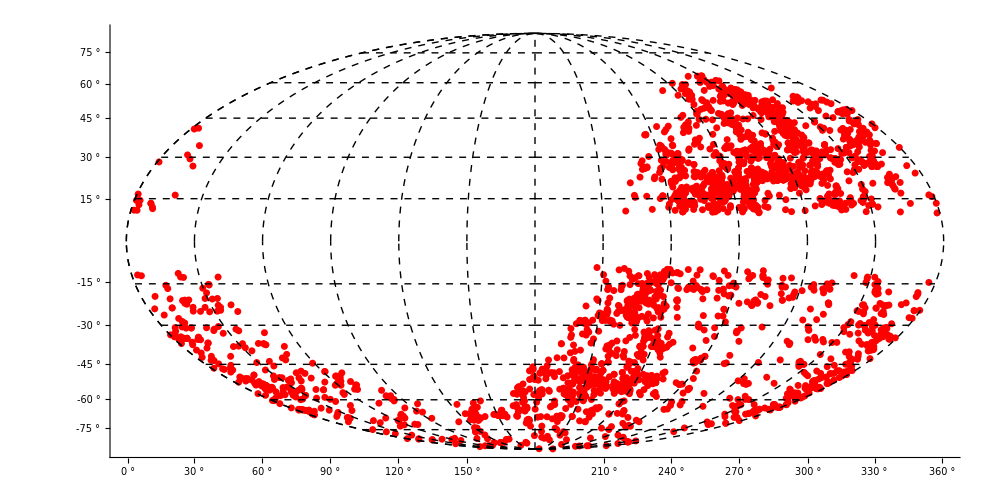

```mathematica
(*Full unbinned low-z sample distribution*)
test=GeoGraphics[{Red,AbsolutePointSize@5,Point[GeoPosition@tabcoordgal]},GeoRange->{{-90,90},{0,360}},GeoGridLinesStyle->Directive[Black,Dashed],GeoProjection->"Mollweide",GeoGridLines->{{-90,90,-75,75,-60,60,-45,45,-30,30,-15,15},{0,30,60,90,120,150,180,210,240,270,300,330,360}},ImageSize->1000,Ticks->{ticksx,ticksy},GeoBackground->White,Axes->True,Background->White,AxesStyle->Black,TicksStyle->Directive[Black,FontSize->19]]
```

```mathematica
Export[NotebookDirectory[]<>"skycov6dFGS.pdf",test,ImageResolution->1000];
```